```mathematica
ψ[n_,x_] := (2^n n! Sqrt[π])^(-1/2) Exp[-x^2/2] HermiteH[n,x]
```

```mathematica
HermiteH[1,x]
```

2 x

```mathematica
Integrate[ψ[3,x] 4 (x - x^3),{x,-Infinity,Infinity}]
```

-24 √6 π^(1/4)

```mathematica
N[%]
```

-78.2662

```mathematica
ψ[0,x]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
driftcoeff[[1]]
```

0.261029

```mathematica
ψ[0,x]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
driftcoeff={0.261029,-12.968365,0.926878,-26.695458,0.724951,-2.495652,-0.990454,20.129598,-1.143489,11.359086};
```

```mathematica
driftfn = Sum[driftcoeff[[i+1]] ψ[i,x],{i,0,Length[driftcoeff]-1}]
```

0.196066 ⅇ^(-x^2/2)-13.7757 ⅇ^(-x^2/2) x+0.246144 ⅇ^(-x^2/2) (-2+4 x^2)-2.8942 ⅇ^(-x^2/2) (-12 x+8 x^3)+0.0277879 ⅇ^(-x^2/2) (12-48 x^2+16 x^4)-0.0302504 ⅇ^(-x^2/2) (120 x-160 x^3+32 x^5)-0.0034657 ⅇ^(-x^2/2) (-120+720 x^2-480 x^4+64 x^6)+0.0188247 ⅇ^(-x^2/2) (-1680 x+3360 x^3-1344 x^5+128 x^7)-0.00026734 ⅇ^(-x^2/2) (1680-13440 x^2+13440 x^4-3584 x^6+256 x^8)+0.000625949 ⅇ^(-x^2/2) (30240 x-80640 x^3+48384 x^5-9216 x^7+512 x^9)

```mathematica
Collect[driftfn,Exp[-x^2/2]]
```

ⅇ^(-x^2/2) (0.00398337+4.628 x+0.74851 x^2-5.53924 x^3-1.48491 x^4+4.01756 x^5+0.736343 x^6-3.35919 x^7-0.0684391 x^8+0.320486 x^9)

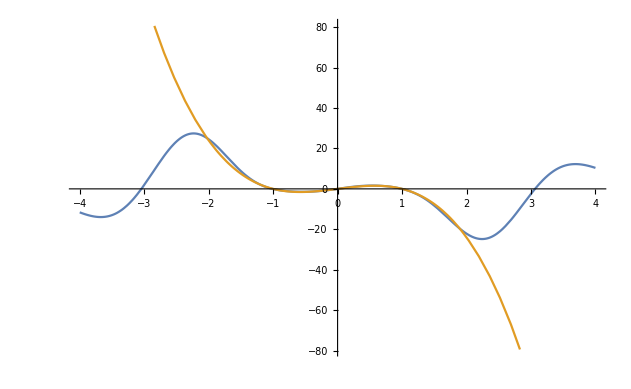

```mathematica
Plot[{driftfn,4 (x - x^3)},{x,-4,4}]
```